```mathematica
(* Mathematica*)
```

```mathematica
Clear[f,g,h,k]
```

```mathematica
allColors=ColorData["Legacy"][[3,1]];
firstCols=Join[{"White","AliceBlue","LightBlue","Cyan","ManganeseBlue","DodgerBlue","Blue","Magenta","Purple","Pink","Tomato","Red","DarkOrange","Orange","DeepNaplesYellow","Gold","Banana","Yellow","LightYellow","Orange","Pink","LightPink","Yellow","LightYellow","LightPink","White","DeepNaplesYellow","Orange","DarkOrange","Tomato","Red","Tomato","Pink","LightPink","DeepNaplesYellow","Orange","DarkOrange","Tomato","White","Pink","Banana","LightBlue","DodgerBlue","Cyan","White","Purple","DarkOrchid","Magenta","ManganeseBlue","DeepNaplesYellow","Orange","DarkOrange","Tomato","GoldOchre","LightPink","Magenta","Green","DarkOrchid","LightSalmon","LightPink","Sienna","Green","Mint","DarkSlateGray","ManganeseBlue","SlateGray","DarkOrange","MistyRose","DeepNaplesYellow","GoldOchre","SapGreen","Yellow","Yellow","Tomato","DeepNaplesYellow","DodgerBlue","Cyan","Red","Blue","DeepNaplesYellow","Green","Magenta","DarkOrchid","LightSalmon","LightPink","Sienna","Green","Mint","DarkSlateGray","ManganeseBlue","SlateGray","DarkOrange","MistyRose","DeepNaplesYellow","GoldOchre","SapGreen","Yellow","LimeGreen"},{"White","AliceBlue","LightBlue","Cyan","ManganeseBlue","DodgerBlue","Blue","Magenta","Purple","Pink","Tomato","Red","DarkOrange","Orange","DeepNaplesYellow","Gold","Banana","Yellow","LightYellow","Orange","Pink","LightPink","Yellow","LightYellow","LightPink","White","DeepNaplesYellow","Orange","DarkOrange","Tomato","Red","Tomato","Pink","LightPink","DeepNaplesYellow","Orange","DarkOrange","Tomato","White","Pink","Banana","LightBlue","DodgerBlue","Cyan","White","Purple","DarkOrchid","Magenta","ManganeseBlue","DeepNaplesYellow","Orange","DarkOrange","Tomato","GoldOchre","LightPink","Magenta","Green","DarkOrchid","LightSalmon","LightPink","Sienna","Green","Mint","DarkSlateGray","ManganeseBlue","SlateGray","DarkOrange","MistyRose","DeepNaplesYellow","GoldOchre","SapGreen","Yellow","Yellow","Tomato","DeepNaplesYellow","DodgerBlue","Cyan","Red","Blue","DeepNaplesYellow","Green","Magenta","DarkOrchid","LightSalmon","LightPink","Sienna","Green","Mint","DarkSlateGray","ManganeseBlue","SlateGray","DarkOrange","MistyRose","DeepNaplesYellow","GoldOchre","SapGreen","Yellow","LimeGreen"}];
cols=ColorData["Legacy",#]&/@Join[firstCols,Complement[allColors,firstCols]];
rotate[theta_]:={{Cos[theta],-Sin[theta]},{Sin[theta],Cos[theta]}};
cr[n_]:=cr[n]=cols[[n]];
```

```mathematica
f[x_]:=-x+1/2/;0<=x<=1/2
f[x_]:=2*x-1/;1/2<x≤1
```

```mathematica
ff[x_]=f[Mod[Abs[x],1]]
```

f[Mod[Abs[x],1]]

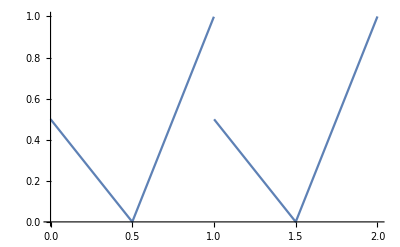

```mathematica
Plot[f[Mod[Abs[x],1]],{x,0,2}]
```

```mathematica
s0=N[Log[2]/Log[3]]
```

0.63093

```mathematica
(*  sigmoid*)
```

```mathematica
g[x_]:=x/;0<=x<=1/2
g[x_]:=-2*x+3/2/;1/2<x≤1
```

```mathematica
gg[x_]=g[Mod[Abs[x],1]]
```

g[Mod[Abs[x],1]]

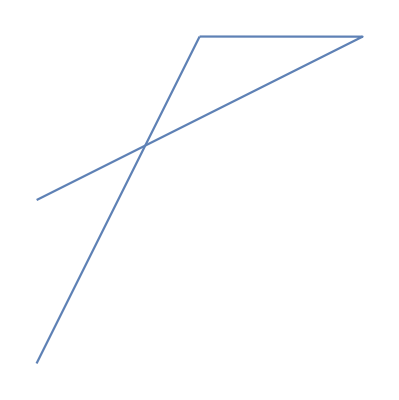

```mathematica
ParametricPlot[{ff[t],gg[t+1/2]},{t,0,1},Axes->False]
```

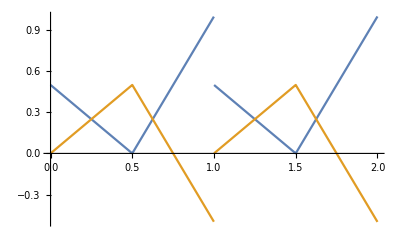

```mathematica
Plot[{ff[t],gg[t]},{t,0,2}]
```

```mathematica
hh[x_]=Sum[ff[3^k*(x)]/3^(s0*k),{k,0,20}];
kk[x_]=Sum[gg[3^k*(x+1/2)]/3^(s0*k),{k,0,20}];
ll[x_]=Sum[ff[3^k*(x+1/2)]/3^(s0*k),{k,0,20}];
```

```mathematica
w1=Table[hh[n/30000],{n,0,30000}];
```

```mathematica
w2=Table[kk[n/30000],{n,0,30000}];
```

```mathematica
ListLinePlot[{w1,w2},ImageSize->Full];
```

```mathematica
aa=Flatten[ParallelTable[{i*kk[n/50000],j*hh[n/50000],k*ll[n/50000]},{i,-1,1,2},{j,-1,1,2},{k,-1,1,2},{n,0,50000}],3];
```

```mathematica
Length[aa]
```

400008

```mathematica
g0=ListPointPlot3D[aa,AspectRatio->1,ColorFunction->Hue,ImageSize->2000,PlotRange->All,ViewPoint->{2,2,2},Background->Black];
```

$Aborted

```mathematica
dlst=ParallelTable[1+Mod[Floor[1+(1+Floor[6*Norm[aa[[i]]]])/(Abs[Cos[Arg[aa[[i,1]]+I*aa[[i,2]]]]]+Abs[Sin[Arg[aa[[i,1]]+I*aa[[i,2]]]]])],Length[cols]],{i,Length[aa]}];
Min[dlst]
Max[dlst]
```

7

16

```mathematica
ptlst=Point[Developer`ToPackedArray[aa],VertexColors->Developer`ToPackedArray[cr/@dlst]];
```

```mathematica
g2=Graphics3D[{PointSize[.001],ptlst},AspectRatio->1,ImageSize->2000,Axes->False,Background->Black,PlotRange->All,ViewPoint->{2,2,2}];
```

```mathematica
Export["biscuit_Kiesswetter_Cycle_scale3_triple_sign_color.jpg",{g0,g2}]
(*end*)
```